```mathematica
capacityList={14,17,11,6,18,4,22,20,19,16,10,13,9,7,5,12,23,3,2,21,15,8,24,1};
tags=CharacterRange["a","x"];
```

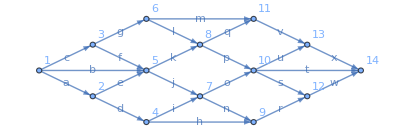

```mathematica
flowGraph=EdgeTaggedGraph[
Range[14],
{
1->2,1->5,1->3,
2->4,2->5,
3->5,3->6,
4->9, 4->7,
5->7, 5->8,
6->8, 6->11,
7->9, 7->10,
8->10, 8->11,
9->12, 
10->12,10->14, 10->13,
11->13,
12->14,
13->14
}->tags,
EdgeCapacity->capacityList,
EdgeLabels->"EdgeTag",
VertexLabels->"Name",
GraphLayout->{"SymmetricLayeredEmbedding",
"Rotation"->90 Degree}
]
```

```mathematica
flowData = FindMaximumFlow[flowGraph, 1, 14, "OptimumFlowData"]
```

OptimumFlowData[…]

```mathematica
untag[DirectedEdge[u_, v_, _]] := DirectedEdge[u,v]
```

```mathematica
flow = AssociationThread[EdgeList[flowGraph],
flowData/@(untag/@EdgeList[flowGraph])]
```

<|12a→8,15b→2,13c→11,24d→0,25e→8,35f→0,36g→11,49h→0,47i→0,57j→8,58k→2,68l→10,611m→1,79n→3,710o→5,810p→12,811q→0,912r→3,1012s→0,1014t→17,1013u→0,1113v→1,1214w→3,1314x→1|>

```mathematica
capacity = AssociationThread[EdgeList[flowGraph], capacityList]
residual = capacity - flow
```

<|12a→14,15b→17,13c→11,24d→6,25e→18,35f→4,36g→22,49h→20,47i→19,57j→16,58k→10,68l→13,611m→9,79n→7,710o→5,810p→12,811q→23,912r→3,1012s→2,1014t→21,1013u→15,1113v→8,1214w→24,1314x→1|>

<|12a→6,15b→15,13c→0,24d→6,25e→10,35f→4,36g→11,49h→20,47i→19,57j→8,58k→8,68l→3,611m→8,79n→4,710o→0,810p→0,811q→23,912r→0,1012s→2,1014t→4,1013u→15,1113v→7,1214w→21,1314x→0|>

```mathematica
saturated = Select[Normal[residual], Last[#] === 0 &]//Map[First]
zeroflow = Select[Normal[flow], Last[#]===0 &]//Map[First]
```

{13c,710o,810p,912r,1314x}

{24d,35f,49h,47i,811q,1012s,1013u}

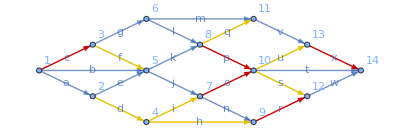

```mathematica
HighlightGraph[flowGraph, {saturated, zeroflow}]
```

Saturated = Red, Zero Flow = Yellow

```mathematica
tail[DirectedEdge[u_, v_, ___]] := u
head[DirectedEdge[u_, v_, ___]] := v
```

```mathematica
edges = EdgeList[flowGraph]
```

{12a,15b,13c,24d,25e,35f,36g,49h,47i,57j,58k,68l,611m,79n,710o,810p,811q,912r,1012s,1014t,1013u,1113v,1214w,1314x}

Recursively label - check if the tail is in X, and not at capacity, then add the head, or if the head is in X, and flow is not 0, add the tail

```mathematica
xStep[X_] :=
Sort@DeleteDuplicates@
Join[X,
head/@Select[edges,
MemberQ[X, tail[#]] &&
!MemberQ[saturated, #] &],
tail/@Select[edges,
MemberQ[X, head[#]] &&
!MemberQ[zeroflow, #] &]]
```

```mathematica
lastStep = xStep[{1}]
```

{1,2,5}

Loop until the next step is the same as the last step

```mathematica
While[xStep[lastStep] != lastStep, lastStep=xStep[lastStep]]
```

```mathematica
X = lastStep
```

{1,2,3,4,5,6,7,8,9,11,13}

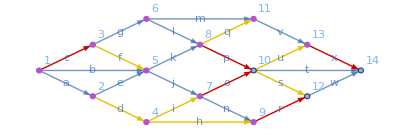

```mathematica
HighlightGraph[flowGraph, {saturated, zeroflow, X}]
```

```mathematica
edgeCut = Select[edges,
MemberQ[X, tail[#]] && !MemberQ[X, head[#]]&]
```

{710o,810p,912r,1314x}

Now Highlight the graph, purple is the labelled edges, Orange the cut set, red the saturated, and yellow zero flow

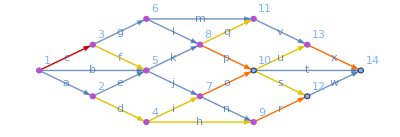

```mathematica
HighlightGraph[flowGraph, {saturated, zeroflow, X, edgeCut}]
```

```mathematica
flow
```

<|12a→8,15b→2,13c→11,24d→0,25e→8,35f→0,36g→11,49h→0,47i→0,57j→8,58k→2,68l→10,611m→1,79n→3,710o→5,810p→12,811q→0,912r→3,1012s→0,1014t→17,1013u→0,1113v→1,1214w→3,1314x→1|>

```mathematica
maxFlow = Total[flow /@ edgeCut]
```

21

```mathematica
edgeCut
```

{710o,810p,912r,1314x}